```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/scavgf/Documents/GaudinModel

```mathematica
Do[
dataz=Import["./dataPlot/propagator-Omega=0.0-N="<>ToString[ix]<>"-D-400-Nt=500-Dt=0.03-lambda=1.0-ep=1.0e-6-Od=2.dat"];
Subscript[Sz400, ix]=appendt[Table[data[[-1]]/2,{data,dataz}],0.03];,
{ix,1,49}]
Do[
Subscript[BD400, ix]=Import["./dataPlot/BD-Omega=0.0-N="<>ToString[ix]<>"-D-400-Nt=500-Dt=0.03-lambda=1.0-ep=1.0e-6-Od=2.dat"][[1]];,
{ix,1,49}]
```

```mathematica
Do[
dataz=Import["./dataPlot/propagator-Omega=0.0-N="<>ToString[ix]<>"-D-300-Nt=500-Dt=0.03-lambda=1.0-ep=1.0e-6-Od=2.dat"];
Subscript[Sz300, ix]=appendt[Table[data[[-1]]/2,{data,dataz}],0.03];,
{ix,1,49}]
Do[
Subscript[BD300, ix]=Import["./dataPlot/BD-Omega=0.0-N="<>ToString[ix]<>"-D-300-Nt=500-Dt=0.03-lambda=1.0-ep=1.0e-6-Od=2.dat"][[1]];,
{ix,1,49}]
```

```mathematica
Do[
dataz=Import["./dataPlot/propagator-Omega=0.0-N="<>ToString[ix]<>"-D-200-Nt=500-Dt=0.03-lambda=1.0-ep=1.0e-6-Od=2.dat"];
Subscript[Sz200, ix]=appendt[Table[data[[-1]]/2,{data,dataz}],0.03];,
{ix,1,49}];
Do[
Subscript[BD200, ix]=Import["./dataPlot/BD-Omega=0.0-N="<>ToString[ix]<>"-D-200-Nt=500-Dt=0.03-lambda=1.0-ep=1.0e-6-Od=2.dat"][[1]];,
{ix,1,49}]
```

```mathematica
Do[
dataz=Import["./dataPlot/propagator-Omega=0.0-N="<>ToString[ix]<>"-D-100-Nt=500-Dt=0.03-lambda=1.0-ep=1.0e-6-Od=2.dat"];
Subscript[Sz100, ix]=appendt[Table[data[[-1]]/2,{data,dataz}],0.03];,
{ix,1,49}];
Do[
Subscript[BD100, ix]=Import["./dataPlot/BD-Omega=0.0-N="<>ToString[ix]<>"-D-100-Nt=500-Dt=0.03-lambda=1.0-ep=1.0e-6-Od=2.dat"][[1]];,
{ix,1,49}]
```

```mathematica
Clear[Sz400]
```

```mathematica
n=49;
Jk=Table[√((6n)/(2 n^2+3*n+1))(n+1-i)/n,{i,1,49}];
appendt[list_,dt_]:=Join[{Table[ix*dt,{ix,1,Length@list}]},{list}]ᵀ;
renorm[data_,x_]:={x*data[[All,1]],data[[All,2]]}ᵀ
```

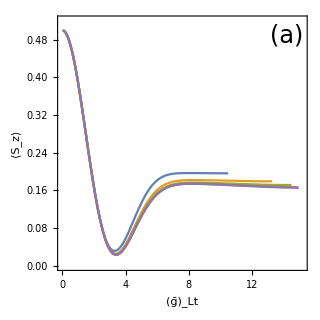

```mathematica
p1=ListLinePlot[Table[renorm[Subscript[Sz400, ix],Norm[Jk[[1;;ix]]]],{ix,{10,20,30,40,49}}],PlotRange->{{0,15.2},{0,0.52}},Frame->True,FrameLabel->{"(ḡ)_Lt","⟨S_z⟩"},LabelStyle->Directive[20, FontFamily->"Times New Roman",Black],AspectRatio->1,ImageSize->320,Epilog->Inset[Style["(a)",{24,FontFamily->"Times New Roman"},Background->White],{14.2,0.49}]]
```

```mathematica
p2=ListLinePlot[Table[renorm[appendt[Subscript[BD400, ix][[1;;350]],0.015],Norm[Jk[[1;;ix]]]],{ix,{10,20,30,40,49}}],PlotRange->{{0,4.5},{0,420}},Frame->True,FrameLabel->{"(ḡ)_Lt","D_t"},PlotLegends->Placed[{"L=10","L=20","L=30","L=40","L=49"},{0.8,0.32}],LabelStyle->Directive[20, FontFamily->"Times New Roman",Black],AspectRatio->1.05,ImageSize->320,
Epilog->Inset[Style["(b)",{24,FontFamily->"Times New Roman"},Background->White],{4.2,394}]];
(*Corollary 2.1*)
ϵ=0.03/2;
d=2;
P20aux=Plot[d^4 t/ϵ,{t,ϵ,4},PlotStyle->{Black,Dashed},PlotRange->{{0,4},All}];
```

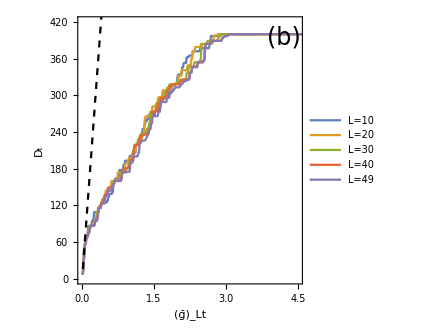

```mathematica
p2=Show[p2,P20aux]
```

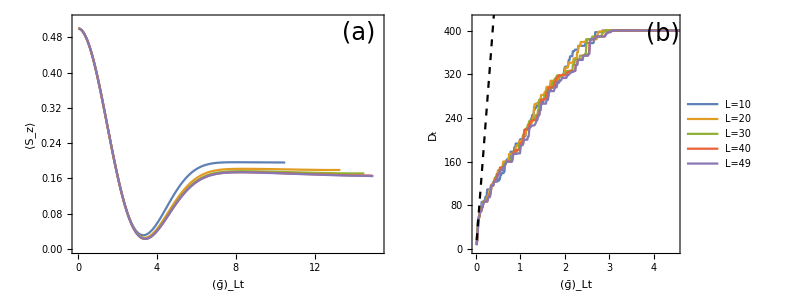

```mathematica
Px=Grid[{{p1,p2}}]
```

```mathematica
Export["Gaudin.pdf",Px]
```

Gaudin.pdf

## Comparison of the results obtained from different cutoff

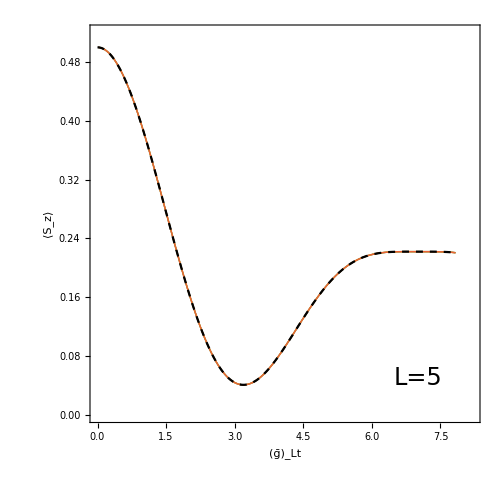

```mathematica
szty=Subscript[szt, 5];
(*Run ExactDataN49.nb first*)
szty[[All,2]]=szty[[All,2]]/2;
p11=ListLinePlot[{renorm[Subscript[Sz100, 5][[270;;All]],Norm[Jk[[1;;5]]]],renorm[Subscript[Sz200, 5][[270;;All]],Norm[Jk[[1;;5]]]],renorm[Subscript[Sz300, 5][[270;;All]],Norm[Jk[[1;;5]]]],renorm[Subscript[Sz400, 5][[270;;All]],Norm[Jk[[1;;5]]]],renorm[szty,Norm[Jk[[1;;5]]]]},PlotRange->{{6.0,8},{0.218,0.223}},Frame->True,LabelStyle->Directive[20, FontFamily->"Times New Roman",Black],PlotStyle->{Thick,Thick,Thick,Thick,{Black,Dashed}},AspectRatio->1,ImageSize->270];
p10=ListLinePlot[{renorm[Subscript[Sz100, 5],Norm[Jk[[1;;5]]]],renorm[Subscript[Sz200, 5],Norm[Jk[[1;;5]]]],renorm[Subscript[Sz300, 5],Norm[Jk[[1;;5]]]],renorm[Subscript[Sz400, 5],Norm[Jk[[1;;5]]]],renorm[szty,Norm[Jk[[1;;5]]]]},PlotRange->{{0,8.2},{0.0,0.52}},Frame->True,FrameLabel->{"(ḡ)_Lt","⟨S_z⟩"},LabelStyle->Directive[24, FontFamily->"Times New Roman",Black],AspectRatio->1,ImageSize->500,Epilog->{Inset[p11,{5,0.37}],Inset[Style[Framed["L=5"],24,FontFamily->"Times New Roman"],{7,0.05}]},PlotStyle->{Thick,Thick,Thick,Thick,{Black,Dashed}}]
```

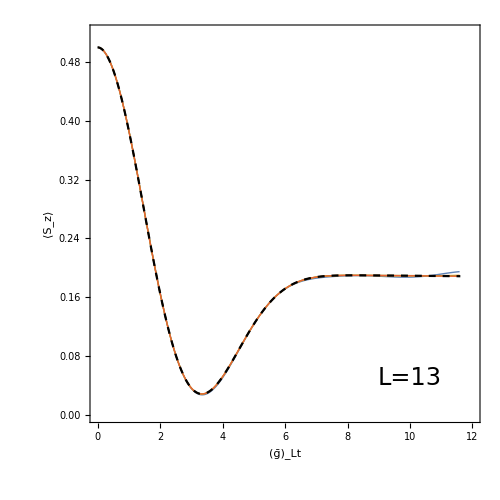

```mathematica
ix=13;
szty=Subscript[szt, ix];
szty[[All,2]]=szty[[All,2]]/2;
p21=ListLinePlot[{renorm[Subscript[Sz100, ix][[270;;All]],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz200, ix][[270;;All]],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz300, ix][[270;;All]],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz400, ix][[270;;All]],Norm[Jk[[1;;ix]]]],renorm[szty,Norm[Jk[[1;;ix]]]]},PlotRange->{{6,12},{0.186,0.19}},Frame->True,LabelStyle->Directive[20, FontFamily->"Times New Roman",Black],AspectRatio->1,ImageSize->270,PlotStyle->{Thick,Thick,Thick,Thick,{Black,Dashed}}];
p20=ListLinePlot[{renorm[Subscript[Sz100, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz200, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz300, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz400, ix],Norm[Jk[[1;;ix]]]],renorm[szty,Norm[Jk[[1;;ix]]]]},PlotRange->{{0,12},{0.0,0.52}},Frame->True,FrameLabel->{"(ḡ)_Lt","⟨S_z⟩"},LabelStyle->Directive[24, FontFamily->"Times New Roman",Black],AspectRatio->1,ImageSize->500,Epilog->{Inset[p21,{8,0.36}],Inset[Style[Framed["L=13"],24,FontFamily->"Times New Roman"],{10,0.05}]},PlotStyle->{Thick,Thick,Thick,Thick,{Black,Dashed}}]
```

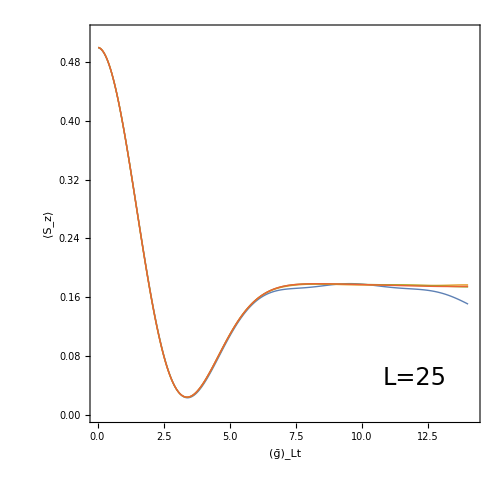

```mathematica
ix=25;
p31=ListLinePlot[{renorm[Subscript[Sz100, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz200, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz300, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz400, ix],Norm[Jk[[1;;ix]]]]},PlotRange->{{6,14.2},{0.172,0.180}},Frame->True,LabelStyle->Directive[20, FontFamily->"Times New Roman",Black],AspectRatio->1,PlotStyle->{Thick,Thick,Thick,Thick,Dashed},ImageSize->270];
p30=ListLinePlot[{renorm[Subscript[Sz100, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz200, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz300, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz400, ix],Norm[Jk[[1;;ix]]]]},PlotRange->{{0,14.2},{0.0,0.52}},Frame->True,FrameLabel->{"(ḡ)_Lt","⟨S_z⟩"},LabelStyle->Directive[24, FontFamily->"Times New Roman",Black],ImageSize->500,Epilog->{Inset[p31,{9,0.36}],Inset[Style[Framed["L=25"],24,FontFamily->"Times New Roman"],{12,0.05}]},PlotStyle->{Thick,Thick,Thick,Thick,{Black,Dashed}},AspectRatio->1]
```

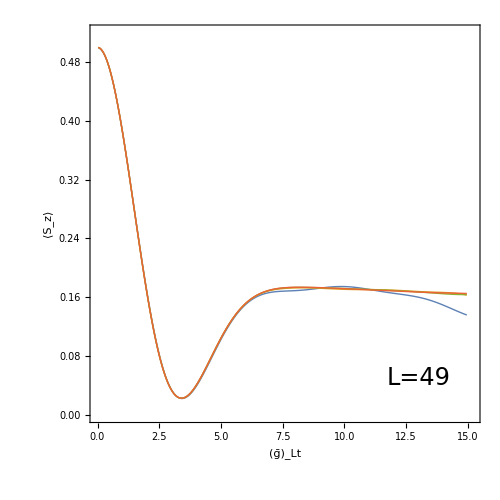

```mathematica
ix=49;
p41=ListLinePlot[{renorm[Subscript[Sz100, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz200, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz300, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz400, ix],Norm[Jk[[1;;ix]]]]},PlotRange->{{6,15.2},{0.16,0.176}},Frame->True,LabelStyle->Directive[20, FontFamily->"Times New Roman",Black],AspectRatio->1,PlotStyle->{Thick,Thick,Thick,Thick,Dashed},ImageSize->270];
p40=ListLinePlot[{renorm[Subscript[Sz100, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz200, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz300, ix],Norm[Jk[[1;;ix]]]],renorm[Subscript[Sz400, ix],Norm[Jk[[1;;ix]]]]},PlotRange->{{0,15.2},{0.0,0.52}},Frame->True,FrameLabel->{"(ḡ)_Lt","⟨S_z⟩"},LabelStyle->Directive[24, FontFamily->"Times New Roman",Black],ImageSize->500,Epilog->{Inset[p41,{9,0.36}],Inset[Style[Framed["L=49"],24,FontFamily->"Times New Roman"],{13,0.05}]},PlotStyle->{Thick,Thick,Thick,Thick,{Black,Dashed}},AspectRatio->1]
```

```mathematica
p50=LineLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4],{Black,Dashed}},{Style["D_c=100",FontFamily->"Times New Roman",20],Style["D_c=200",FontFamily->"Times New Roman",20],Style["D_c=300",FontFamily->"Times New Roman",20],Style["D_c=400",FontFamily->"Times New Roman",20],Style["exact",FontFamily->"Times New Roman",20]},LegendMarkerSize->50]
```

```mathematica
P5=Grid[{{p10,p20,p50},{p30,p40,SpanFromAbove}}]
```

-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
Export["GM-Com.pdf",P5]
```

GM-Com.pdf

## collapsing of the increasing of bond dimension

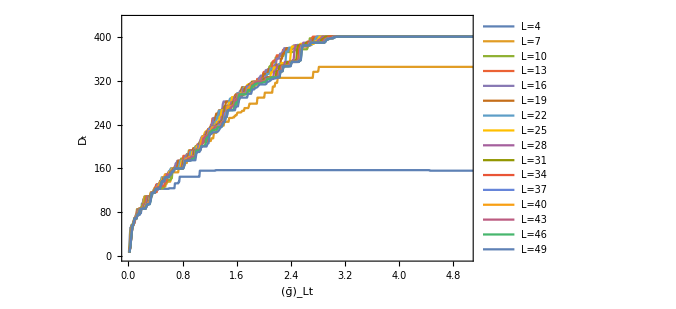

```mathematica
p1=ListLinePlot[Table[renorm[appendt[Subscript[BD400, ix][[1;;999]],0.015],Norm@Jk[[1;;ix]]],{ix,4,49,3}],PlotRange->{{0,5},{0,430}},Frame->True,FrameLabel->{"(ḡ)_Lt","D_t"},LabelStyle->Directive[20, FontFamily->"Times New Roman",Black],PlotLegends->LineLegend[Table["L="<>ToString[ix],{ix,4,49,3}],LegendLayout->{"Column",2}],ImageSize->500]
```

```mathematica
Export["GM-Collapse.pdf",p1]
```

GM-Collapse.pdf